```mathematica
Exit[]
```

# Non singlet sector

Here  we  construct the approximation for the non singlet quantities : gqq3nsp, gqq3nsm, gqq3nss.
NOTE: 	s is defined as ns_s = ns_v - ns_m. It contains parts proportional only to nf and nf^2.
		It vanishes in the large nc limit. (N -> Infinity, it goes to 0) 
 
	•	Limits for N = 0 are taken from 2202.10362, see ancillary file provided and Eq. 3.3, 3.8, 3.9, 3.10 :
  		All the expression have the accuracy O (1/N) and are given in the large colour limit, where p,m,v are all equal .  
	• 	Low N odd (1, 3, 5, 7,9,11,13,15,(17)) moments are taken from  1707.08315.
	•   	Large N limit is given in Eq 2.17 of 1707.08315. 
		The approximation has accuracy O(1/N^2) and fix the terms  Log[N], Log[N]/N, 1/N. 
		According to 1707.08315 terms with Log[N]^k , k> 2 are not present in the expansion. 
	     	The calculation of the QCD cusp is the same as the singlet sector and is provided in 1911.10174, see ancillary file and "qcd_cusp.m"  	
   	     	But looking at the expression of   gqq0 we believe A_k * S[1, N] , S[1,N]/N 1/N to be more accurate expansion.
	• 	The part proportional to nf^3, common for all the p,m,v (s is then vanishing) and is taken exact for Eq 3.6 of 1610.07477 and its ancillary file
	• 	For m,p: the part proportional to nf^2 are also given exact form Eq 2.12, 3.1, 3.2, 3.3, 3.4 of 1610.07477 and its ancillary file
	• 	For s: The part proportional to nf^2 are also taken exact form Eq 3.5 of 1610.07477 and its ancillary file

```mathematica
<<"/Users/giacomomagni/Documents/Wolfram Mathematica/Sigma.m"
<<"/Users/giacomomagni/Documents/Wolfram Mathematica/HarmonicSums.m"
```

Sigma - A summation package by Carsten Schneider — © RISC —  V 2.86 (June 15, 2021)  Help

HarmonicSums by Jakob Ablinger — © RISC — Version 1.0(30/03/21)Help

```mathematica
here = NotebookDirectory[];
Get[StringJoin[here, "constants.m"]]
```

```mathematica
(* Non singlet, large nf exact parts *)
Get[StringJoin[here, "ns_nf1_nf0.m"]]
Get[StringJoin[here, "ns_nf3_nf2.m"]]
(* Singlet, asymptotic N-> Infinity, large nc limit *)
Get[StringJoin[here, "qcd_cusp.m"]]
Get[StringJoin[here, "ns_largeN.m"]]
Get[StringJoin[here, "gamma_thr.m"]]
(* Non singlet, asymptotic N-> 0, large nc limit *)
Get[StringJoin[here, "ns_smallN.m"]]
(* Non singlet, moments *)
Get[StringJoin[here, "gqq3nsp.m"]]
Get[StringJoin[here, "gqq3nsm.m"]]
Get[StringJoin[here, "gqq3nss.m"]]
```

```mathematica
Get[StringJoin[here, "fitting_utils.m"]]
Get[StringJoin[here, "plotting_utils.m"]]
Get[StringJoin[here, "saving_utils.m"]]
```

## Large nf parts (nf^3,nf^2)

Main reference: 1610.07477,  we follow Eq. 2.12, 3.1, 3.2, 3.3, 3.4, 3.5,3.6
The part proportional to nf^3 is already ok.
The part proportional to nf^2 has to be simplified to get rid of some harmonics. In particular:
	•	NS+_nf^2 = A_3 cf^2 + (ca-2 cf)cf B3, 
		•	A3 is given exact, since all the ingredients are available
		•	B3 is parametrized since some harmonics of weight 5 are not available
	•	NS+ = A_3 cf^2 + (ca-2 cf)cf (B3+ deltaB3)
	•	deltaB3 is taken exact, since all the ingredients are available
	•	NS,s is taken exact, since all the ingredients are available

### Plotting routines

```mathematica
PlotNvals[moments_, fexa_, nfpart_, singlet_, QCDconst_]:=Module[{Nmin, nvals,title},
	If[singlet, Nmin=2, Nmin=1];
	nvals = Range[Nmin, 2 Length[moments],2];
	title = StringForm["relative diff N moment-fexa, Part prop to nf^``.", nfpart];
	ListPlot[
		MapThread[{#1, (#2 - fexa)/fexa /. QCDconst /. ZetaRules /. n -> #1} &, {nvals, Coefficient[moments,nf,nfpart]}], 
		PlotLabel->title
	]
];
```

### Nf^3

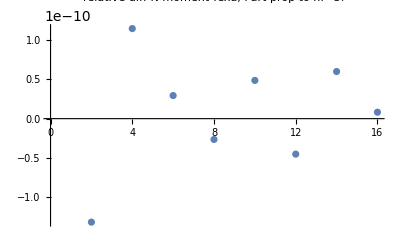

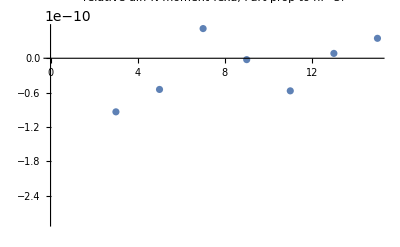

```mathematica
momentlist = {gqq3nspN2, gqq3nspN4, gqq3nspN6, gqq3nspN8,gqq3nspN10,gqq3nspN12,gqq3nspN14,gqq3nspN16};
PlotNvals[momentlist, gqq3nsnf3, 3, True, QCDConstantsRules]
momentlist = {gqq3nsmN1, gqq3nsmN3, gqq3nsmN5, gqq3nsmN7,gqq3nsmN9,gqq3nsmN11,gqq3nsmN13,gqq3nsmN15};
PlotNvals[momentlist, gqq3nsnf3, 3, False, QCDConstantsRules]
```

### Nf^2

```mathematica
(* Symplify some other harmonics sums *)
harmonics5rules = {
           S[1, 4, n] -> SRemoveLeadingIndex[S[1, 4, n]],
           S[1, -4, n] -> SRemoveLeadingIndex[S[1, -4, n]],
           S[3, 2, n] -> SRemoveLeadingIndex[S[3, 2, n]],
           S[3, -2, n] -> SRemoveLeadingIndex[ S[3, -2, n]],
           S[1, 3, 1, n] -> SRemoveLeading1[S[1, 3, 1, n]], 
           S[1, -2, 1, n] -> SRemoveLeadingIndex[S[1, -2, 1, n]]
} //. harmonics234 /. harmonics /. harmonicminus;
```

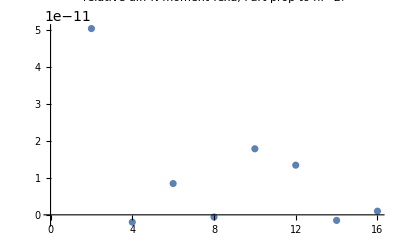

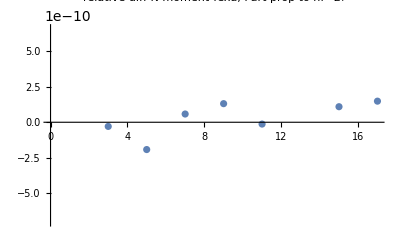

```mathematica
(* check *)
momentlist = {gqq3nspN2, gqq3nspN4, gqq3nspN6, gqq3nspN8,gqq3nspN10,gqq3nspN12,gqq3nspN14,gqq3nspN16};
PlotNvals[momentlist, gqq3nspnf2, 2, True, QCDConstantsRules]

momentlist = {gqq3nssN1, gqq3nssN3, gqq3nssN5, gqq3nssN7,gqq3nssN9,gqq3nssN11,gqq3nssN13,gqq3nssN15,gqq3nssN17};
PlotNvals[momentlist, gqq3nssnf2, 2, False, QCDConstantsRules]
```

#### Common part

```mathematica
(* A_3 *)
gqq3nsnf2A //. harmonics234  //. harmonics5rules  /. harmonics5 /. harmonics /. harmonicminus // Simplify
```

1/81 (1143-1728/(1+n)^5-864/(n^5 (1+n)^5)-2736/(1+n)^4-7088/(1+n)^3-40920/(1+n)^2+20681/(n+n^2)+(1440 S1)/(n^4 (1+n)^4)-10072 S2+(6144 S2)/(1+n)^2-(3328 S2)/(n+n^2)+1920 S2^2+(16 (59+54 S1+72 S2))/(n^3 (1+n)^3)+2304 S23+7968 S3-(1152 S3)/(1+n)^2-(384 S3)/(n+n^2)-3456 S2 S3+3840 S31+(576 S31)/(n+n^2)+2304 S311-3792 S4-(288 S4)/(n+n^2)-4608 S41+576 S5-2376 z3-(1728 z3)/(1+n)^2-(2880 z3)/(n+n^2)-1728 S2 z3+(-4550-7312 S1+96 S2+576 S3+864 z3)/(n^2 (1+n)^2)+2 S1 (2119-1728/(1+n)^4-576/(1+n)^3-3392/(1+n)^2+3392/(n+n^2)-608 S2+960 S3-576 S31+288 S4+2880 z3-1296 z4)+1944 z4+(1296 z4)/(n+n^2))

#### NS +, B3 parametrization

This part contains weight 5 harmonics sums, which are not yet available, so we parametrize the full expression.

```mathematica
(* B_3p, here you need to parametrize the missing parts *)
PlotFitExact[H_, f_,min_,max_]:=Module[{g1, g2}, 
	 (*plot fit and exact series *)
	g1 = ListPlot[Table[H, {n, min, max}]];
	g2 = Plot[f, {n,min,max}, PlotStyle->Red];
	Show[g1,g2]
]

PlotRelDiff[H_, f_,min_,max_]:=Module[{ht}, 
	(* relative difference *)
	ListPlot[ Table[(H - f)/ H * 100 /.QCDConstantsRules/. HarmonicRules /.ZetaRules, {n,min,max}]]
]

ParametrizeToExa[fexa_, basis_, Nmin_, Nmax_]:=Module[{fitted},
	fitted = Fit[Table[fexa, {n,Nmin, Nmax}],basis,n];
	fitted
]

TestForOneValue[H_, f_, val_]:=Module[{},
	Print["Relative difference (%): ", (f - H )/H * 100 //. n -> val // N]
]
```

```mathematica
basis = {
		1,
   	PolyGamma[0, n+1] + EulerGamma,
   	(PolyGamma[0, n+1] + EulerGamma)/n,
   	(PolyGamma[0, n+1] + EulerGamma)/n^2,
   	1/(n(n+1))^4, 1/(n+1)^4,
   	1/(n(n+1))^3, 1/(n+1)^3
 };
f5unknown = gqq3nspnf2B /. ZetaRules;
f5param = ParametrizeToExa[f5unknown,basis,1, 200];
PlotFitExact[f5unknown,f5param, 1, 500]
PlotRelDiff[f5unknown,f5param, 1, 500]
TestForOneValue [f5unknown,f5param, 10]
f5param /. HarmonicRules
```

$Aborted

$Aborted

$Aborted

Relative difference (%): 0.812472 (-123.081+f5param)

f5param

Relative difference (%): -0.00164756

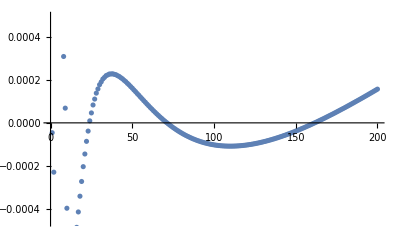

```mathematica
(* worst accuracy occurs at n=6 *)
TestForOneValue [f5unknown, f5param, 2]
(* test with the full nf^2 part *)
PlotRelDiff[gqq3nsnf2A cf^2 + (ca - 2 cf) cf f5param, gqq3nspnf2, 1, 200]
```

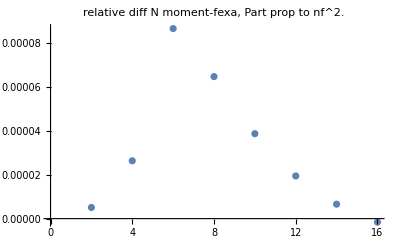

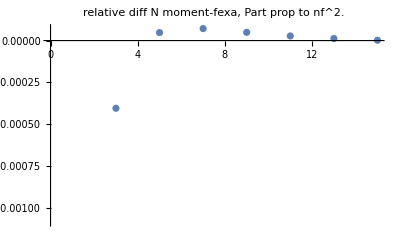

```mathematica
(* check *)
momentlist = {gqq3nspN2, gqq3nspN4, gqq3nspN6, gqq3nspN8, gqq3nspN10, gqq3nspN12, gqq3nspN14, gqq3nspN16};
PlotNvals[momentlist, gqq3nsnf2A cf^2 + (ca - 2 cf) cf f5param, 2, True]
momentlist = {gqq3nsmN1, gqq3nsmN3, gqq3nsmN5, gqq3nsmN7, gqq3nsmN9, gqq3nsmN11, gqq3nsmN13, gqq3nsmN15};
PlotNvals[momentlist, gqq3nsnf2A cf^2 + (ca - 2 cf) cf (f5param + gqq3nsmnf2B - gqq3nspnf2B) , 2, False]
```

#### Delta NSp - NSm

```mathematica
(* delta B_3 *)
gqq3nsmnf2B - gqq3nspnf2B//. harmonics234 /. harmonics /. harmonicminus
```

256/(9 (1+n)^5)-32/(3 n^5 (1+n)^5)-832/(9 (1+n)^4)-320/(27 n^4 (1+n)^4)-1856/(27 (1+n)^3)+4336/(81 n^3 (1+n)^3)-1952/(27 (1+n)^2)-2800/(81 n^2 (1+n)^2)+1744/(27 n (1+n))+(128 S1)/(3 (1+n)^4)-(128 S1)/(9 n^4 (1+n)^4)+(256 S1)/(9 (1+n)^3)-(320 S1)/(27 n^3 (1+n)^3)+(256 S1)/(9 (1+n)^2)+(1568 S1)/(27 n^2 (1+n)^2)-(224 S1)/(9 n (1+n))-(64 (S1^2+S2))/(9 n^3 (1+n)^3)-(128 (S1^2+S2))/(9 n^2 (1+n)^2)-(64 Sm2)/(9 n^3 (1+n)^3)-(128 Sm2)/(9 n^2 (1+n)^2)

#### NS sea

```mathematica
gqq3nssnf2 //. harmonics5rules //. harmonics234 /. harmonics5 /. harmonics /. harmonicminus // Simplify
```

160/27 (40/(1+n)^6-8/(n^6 (1+n)^6)-16/(1+n)^5-24/(n^5 (1+n)^5)+108/(1+n)^4+36/(n^4 (1+n)^4)+112/(1+n)^3+168/(n^3 (1+n)^3)+144/(1+n)^2+174/(n^2 (1+n)^2)-32/(3 (2+n)^2)-208/(3 (-2+n+n^2))-64/(n+n^2)+((-32+192 n+1512 n^2+3768 n^3+5208 n^4+4140 n^5+2077 n^6+827 n^7+790 n^8+674 n^9+261 n^10+39 n^11) S1)/(2 (-1+n) n^5 (1+n)^5 (2+n)^2)-((12+40 n+73 n^2+64 n^3+30 n^4+6 n^5+16 n^6+12 n^7+3 n^8) (2 S1^2+S2))/(n^4 (1+n)^4 (-2+n+n^2))+((12+8 n+19 n^2+57 n^3+30 n^4+n^5+n^6) S3)/(n^3 (1+n)^3 (-2+n+n^2))+(-12/(n^2 (1+n)^2)+32/(-2+n+n^2)-22/(n+n^2)) S4+((-112-528 n-1112 n^2-1452 n^3-1135 n^4-514 n^5-56 n^6+38 n^7+7 n^8) Sm2)/((-1+n) n^3 (1+n)^4 (2+n)^2)+(4 (8+28 n+98 n^2+201 n^3+207 n^4+112 n^5+41 n^6+9 n^7) Sm21)/((-1+n) n^3 (1+n)^3 (2+n)^2)-(8 (2+n+n^2) (S4+Sm2^2+4 Sm211-Sm22))/((-1+n) n (1+n) (2+n))-(2 (-8+28 n+150 n^2+269 n^3+297 n^4+192 n^5+79 n^6+17 n^7) Sm3)/((-1+n) n^3 (1+n)^3 (2+n)^2)+(8 (28+84 n+99 n^2+82 n^3+42 n^4+14 n^5+3 n^6) (S1 Sm2-Sm21+Sm3))/((-1+n) n^2 (1+n)^3 (2+n)^2)-(2 (4+8 n+11 n^2+6 n^3+3 n^4) (-S31+S4-8 Sm211+4 Sm22+S1 (S3+4 Sm21-2 Sm3)+4 Sm31-3 Sm4))/(n^2 (1+n)^2 (-2+n+n^2))-(4 (2+n+n^2)^2 (S31+2 S1^2 Sm2+S2 Sm2-4 S1 Sm21+4 Sm211-3 Sm22+4 S1 Sm3-4 Sm31+3 Sm4))/(n^2 (1+n)^2 (-2+n+n^2)))

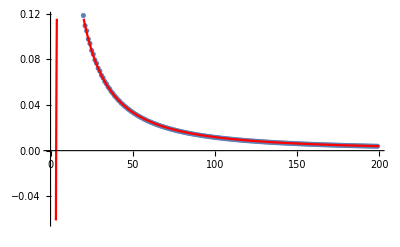

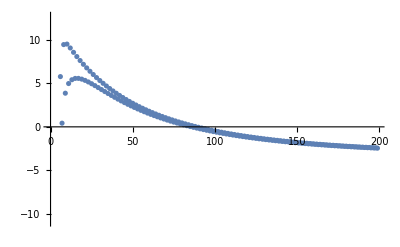

Relative difference (%): -3.86948

-89224.4/n^2-82020.8/(1+n)^4-20592.1/(n^4 (1+n)^4)-61744.1/(1+n)^3+48866./(n^3 (1+n)^3)+(62.3864 (-1/(1+n)+S[1,1+n]))/n^2-(62789.8 (-1/(1+n)^2+S[2,1+n]))/n^2+(159971. (1/2 (2 (-1/(1+n)^3+S[3,1+n])-2 Zeta[3])+Zeta[3]))/n^2

```mathematica
basis = {
      	(PolyGamma[0, n + 1] + EulerGamma)/n^2,
      	(-PolyGamma[1,n+1]+Zeta[2])/n^2,
      	(1/2PolyGamma[2,n+1]+Zeta[3])/n^2,
      	1/(n (n + 1))^4, 1/(n + 1)^4,
      	1/(n (n + 1))^3, 1/(n + 1)^3,
      	1/n^2
};
funknown = gqq3nssnf2 /. ZetaRules;
fparam = ParametrizeToExa[funknown, basis, 2, 100];
PlotFitExact[funknown, fparam, 2, 200]
PlotRelDiff[funknown, fparam, 2, 200]
TestForOneValue [funknown, fparam, 10]
fparam /. HarmonicRules
```

## Non Singlet sector fits

### Fit routines

```mathematica
AdFit[moments_, nfmin_, nfmax_, Nmin_ , asyN0_, asyNinf_]:=Module[{momentslist, nvals},
	 (* Fit the available mellin moments separately for each nf part *)
	 nvals = Range[Nmin, Nmin-1+2 Length[moments],2];
	 momentslist = MapThread[#1 - asyN0 - asyNinf//.n -> #2 &, {moments, nvals}];
	 momentslist = momentslist //. QCDConstantsRules /. ZetaRules // N;
	 flist = MapThread[FitNf[momentslist, #, nvals]&, {Range[nfmin,nfmax]}];
	 nf^Range[nfmin, nfmax].flist
];

FitNf[moments_, nfpart_, nvals_]:=Module[{DataTable,f, Nmin, Nmax, title},
	(* Fit the available mellin moments for a given nf *)
	DataTable = MapThread[{#1,Coefficient[#2,nf, nfpart]}&,{nvals, moments}];
	f = Fit[DataTable, FitBasis, n];
	(* Plot the fitted part *)
	Nmin = 0; 
	Nmax = nvals[[-1]]+2;
	title = StringForm["Prop to nf^``.", nfpart];
	Print[PlotFittedTable[DataTable, f,Nmin,Nmax,title]];
	f /. HarmonicRules
];


MellinInverse[f_] := Module[{temp,fx, f4, f4x},
	(* Mellin inversion *)
	f4 = S[1,n]/n^2;
	f4x = -PolyLog[2,x]+Zeta[2];
	temp = (f - Coefficient[f,f4] f4 ) //Expand; 
	fx = InvMellin[ temp //. QCDConstantsRules /. ZetaRules /. n -> n+1, n, x] /. InvMellinRules /. hrep;
	fx + Coefficient[f,f4] f4x 
];



PlotFittedTable[DataTable_, f_, min_,max_, title_]:=Module[{ g1, g2}, 
	(*plot fit and exact series *)
	g1 = ListPlot[DataTable, PlotMarkers->{Automatic, 10}];
	g2 = Plot[f, {n,min,max}, PlotStyle->Red];
	Show[g1,g2, AxesOrigin->{0,0}, PlotRange->{{min,max}, {Min[DataTable], Max[DataTable]}}, PlotLabel->title]
];


PlotXspaceNonSinglet[title_, fitted_, asyN0_, asyNinf_, NF_: 4, xmax_: 1, fx_: 0, includeparam_: False] := Module[{DoubleLog,Fitted,Asyinf,Total,legend, flist, g1,g2, pifact},
	(* x space plot *)
	DoubleLog = MellinInverse[asyN0];
	Fitted = MellinInverse[fitted] /. Delta[__] -> 0;
	Asyinf = - asyNinf /. Delta[__] -> 0;
	legend = {"small-x (2202.10362)", "Fitted moments", "Large N limit", "Total"};
	Total = DoubleLog + Fitted + Asyinf;
	pifact = 1/(4 Pi)^4;
	flist = { - DoubleLog pifact, -Fitted pifact, -Asyinf pifact, -Total pifact} /. nf -> NF;
	If[includeparam,
		legend = {"small-x (2202.10362)", "Fitted moments", "Large N limit", "Total", "1707.08315 param"};
		flist = { - DoubleLog pifact, - Fitted pifact, - Asyinf pifact, - Total pifact, fx pifact}/. nf -> NF;
	];
	Print[ "Limit for x=1 : ", Series[ - Total /. nf -> NF, {x,1,1}]];
	g1 = LogLinearPlot[
		flist, {x,0.0000001, xmax},
		PlotLegends->legend, PlotLabel->title, ImageSize->Large, AxesLabel->{"x",""}
	];
	g2 = Plot[
		flist, {x,0.0000001, xmax},
		PlotLegends->legend, PlotLabel->title, ImageSize->Large, AxesLabel->{"x",""}
	];
	GraphicsRow[{g1,g2}, ImageSize->Full]
];

PlotRelativeDiff[fexa_, QCDexa_, ffitted_, QCDfitted_, NF_, Nmin_, Nmax_]:=Module[{difflist,nmax, ffitednum, fexanum},
	(* N space relative difference plot *)
	ffitednum = ffitted //. QCDfitted /. ZetaRules;
	fexanum = fexa //. QCDexa /. ZetaRules;
	difflist = Table[( Coefficient[ffitednum,nf,NF] - fexanum)/fexanum *100, {n,Nmin,Nmax}];
	ListPlot[MapThread[{#1, #2}&, {Range[Nmin,Nmax], difflist}], PlotLabel-> StringForm["% difference (fitted-exact)/exact, NF^``",NF]]
];
```

```mathematica
(* Build the large N common limit, note, since B4 is given in the large nc only we can use the result
from 2205.04493 which should be more accurate  *)
B4fullnc =  4^4 Coefficient[gqqdelta, as, 4] /. AdditionalQCDcostantsRules /. QCDConstantsRules /. NumeriCalFactorsRules /. ZetaRules; 
gqq3nsNinf = A4 S[1, n] + B4fullnc + C4 S[1, n]/n  - (D4 - 1/2 A4) 1/n /. QuarkConstants //. QCDConstantsRules;
gqq3nsXinf = A4 1/(1 - x) - B4fullnc Delta[1 - x] + C4 Log[1 - x] + (D4 - A4) /. QuarkConstants  //. QCDConstantsRules;
```

### Gamma qq NS,-

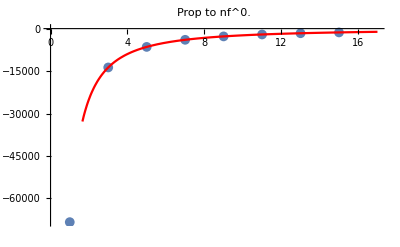

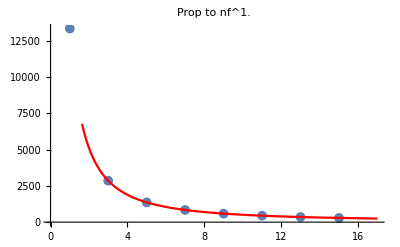

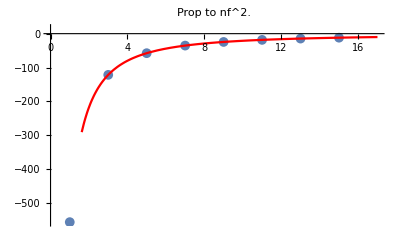

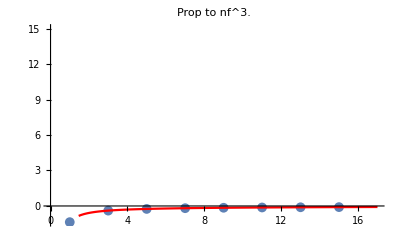

Limit for x=1 : Floor[-Arg[-1+x]/(2 π)] ((0.+350154. ⅈ) (x-1)+O[x-1]^2)+(-3353.35/(x-1)-618.509 (3.27346-7.03842 z2+1. z2^2+3.92526 z3-0.0817578 z2 z3-4.75217 z5-10.3647 Log[1-x])-12883. ((8.32228-13.5898 ⅈ)+14.0801 Log[1-x]+4.63312 Log[1-x]^2+1. Log[1-x]^3-4.32576 Log[-1+x]) (x-1)+O[x-1]^2)

-Graphics-

```mathematica
FitBasis = {
		(* Polynomial basis *) 
		(* 1,
        1/(n+1),1/(n+2),1/(n+3),1/(n+4),
        1/(n+1)^2,
        (PolyGamma[0,n+1]+ EulerGamma)/(n+1),
        (PolyGamma[0,n+1]+ EulerGamma)/n^2 *)
        (* Mellin space basis *) 
        (* 1,
		1/(n+2),
        (PolyGamma[0,n+1]+ EulerGamma)/(n+1),
        (PolyGamma[0,n+1]+ EulerGamma)/(n+1)^2,
        (PolyGamma[0,n+1]+ EulerGamma)/(n+1)^3,
        1/(n+1)^2,
        1/(n+1)^3,
        (PolyGamma[0,n+1]+ EulerGamma)/n^2 *)
        (* x space basis *) 
         1,
		1/(n+3),
		Lm11m1[n],Lm12m1[n],Lm13m1[n],
		1/(n+1)^2,
        1/(n+1)^3,
        (PolyGamma[0,n+1]+ EulerGamma)/n^2
};
Nfmin = 0;
Nfmax = 3;
gqq3nsmFitted = AdFit[
	{gqq3nsmN1, gqq3nsmN3, gqq3nsmN5, gqq3nsmN7,gqq3nsmN9,gqq3nsmN11,gqq3nsmN13,gqq3nsmN15},
	Nfmin, Nfmax, 1, gqq3nsmN0asy, gqq3nsNinf
];

PlotXspaceNonSinglet["(P^(3))_(NS, -)(x), nf=4, series in α_s", gqq3nsmFitted, gqq3nsmN0asy, gqq3nsXinf, 4, 0.99, 0,False]
```

### Gamma qq NS,+

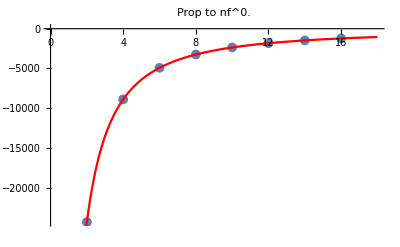

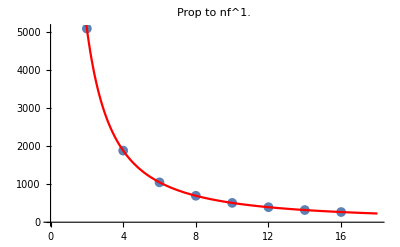

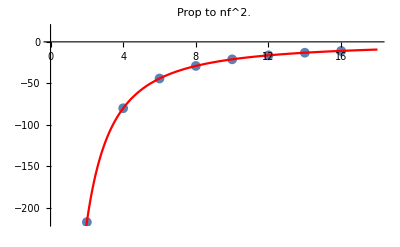

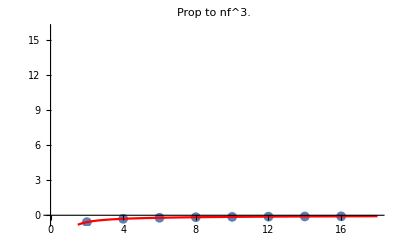

Limit for x=1 : Floor[-Arg[-1+x]/(2 π)] ((0.+190554. ⅈ) (x-1)+O[x-1]^2)+(-3353.35/(x-1)-618.509 (11.8922-7.03842 z2+1. z2^2+3.92526 z3-0.0817578 z2 z3-4.75217 z5-10.3647 Log[1-x])-2345.02 ((9.90401-40.6296 ⅈ)+20.1037 Log[1-x]+5.58845 Log[1-x]^2+1. Log[1-x]^3-12.9328 Log[-1+x]) (x-1)+O[x-1]^2)

-Graphics-

```mathematica
FitBasis = {
		1,
		1/(n+2),
		Lm11m1[n],Lm12m1[n],Lm13m1[n],
		1/(n+1)^2,
        1/(n+1)^3,
        (PolyGamma[0,n+1]+ EulerGamma)/n^2
};
Nfmin = 0;
Nfmax = 3;
gqq3nspFitted = AdFit[
	{gqq3nspN2, gqq3nspN4, gqq3nspN6, gqq3nspN8,gqq3nspN10,gqq3nspN12,gqq3nspN14,gqq3nspN16},
	Nfmin, Nfmax,
	2,
	gqq3nspN0asy,
	gqq3nsNinf 
];
PlotXspaceNonSinglet["(P^(3))_(NS, +)(x), nf=4, series in α_s", gqq3nspFitted, gqq3nspN0asy, gqq3nsXinf, 4, 0.99,0,False]
```

### Comparison with x space parametrization

#### Fast MellinRules

```mathematica
MellinRules={
	Log[1-x] Log[x] -> (S[1,n]-n (π^2/6-S[2,n]))/n^2,
	Log[1-x]^2 -> (S[1,n]^2+S[2,n])/n ,
	x Log[1-x]^2-> (S[1,n+1]^2+S[2,n+1])/(n+1),
	Log[1-x]^3->  -(S[1,n]^3+3 S[1,n] S[2,n]+2 S[3,n])/n,
	x Log[1-x]^3 -> -(S[1,n+1]^3+3 S[1,n+1] S[2,n+1]+2 S[3,n+1])/(n+1),
	Log[1-x] ->  - S[1,n]/n,
	x Log[1-x] -> - S[1,n+1]/(n+1), 
	Log[x]^2/(1-x) -> 2 (1/n^3+1/2 (-2 S[3,n]+2 Zeta[3])),
	Log[x]^3/(1-x) -> -6/n^4-π^4/15+6 S[4,n], 
	Log[x]/(1-x) -> -1/n^2-π^2/6+S[2,n],
	x Log[x]^2-> 2/(n+1)^3, x Log[x]^3-> -6/(n+1)^4, x Log[x]^4 -> 24/(n+1)^5, x Log[x]^5-> - 120/(n+1)^6,x Log[x]-> -1/(n+1)^2, 
	Log[x]-> -1/n^2, Log[x]^2-> 2/n^3, Log[x]^3-> -6/n^4, Log[x]^4 -> 24/n^5, Log[x]^5-> - 120/n^6,Log[x]^6->  6!/n^7,
	
	x^2 -> 1/(n+2), 
	x^3 -> 1/(n+3),
	x^4 -> 1/(n+4),
	x -> 1/(n+1)
};
```

#### NS, -

```mathematica
constpartm = 59302.69550000001-10377.70081 nf+429.14079999999996 nf^2-2.426296 nf^3;
gqq3nsmexa = -(
  + (((P3NSMA -constpartm) //Expand ) /.MellinRules ) + constpartm 1/n
  + ((P3NSMB  // Expand ) /. 1/(1-x) ->  -S[1,n-1])
  (* 
  The contribution prop to Log[1-x] has alrady been included in the prescriprion 
  of Mellin transform 1/(1-x)_{+} with (x(n-1)-1), so can be removed.
  *)
 + ((P3NSMC  // Expand ) /. Log[1-x] -> 0)
);
PlotXspaceNonSinglet["(P^(3))_(NS, -)(x), nf=4, series in α_s", gqq3nsmFitted, gqq3nsmN0asy, gqq3nsXinf, 4, 0.99, (P3NSMA + P3NSMB + P3NSMC),True]
```

Limit for x=1 : Floor[-Arg[-1+x]/(2 π)] ((0.+350154. ⅈ) (x-1)+O[x-1]^2)+(-3353.35/(x-1)-618.509 (3.27346-7.03842 z2+1. z2^2+3.92526 z3-0.0817578 z2 z3-4.75217 z5-10.3647 Log[1-x])-12883. ((8.32228-13.5898 ⅈ)+14.0801 Log[1-x]+4.63312 Log[1-x]^2+1. Log[1-x]^3-4.32576 Log[-1+x]) (x-1)+O[x-1]^2)

-Graphics-

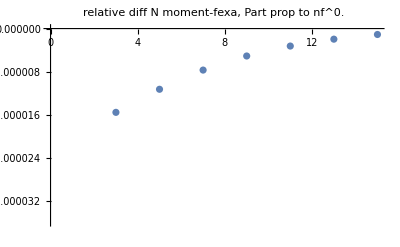

```mathematica
PlotNvals[{gqq3nsmN1, gqq3nsmN3, gqq3nsmN5, gqq3nsmN7,gqq3nsmN9,gqq3nsmN11,gqq3nsmN13,gqq3nsmN15}, Coefficient[gqq3nsmexa,nf,0], 0, False, QCDConstantsRules]
```

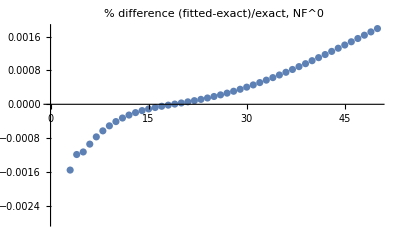

```mathematica
NF=0;
PlotRelativeDiff[Coefficient[gqq3nsmexa,nf,NF],QCDConstantsRules,  gqq3nsmFitted + gqq3nsmN0asy + gqq3nsNinf,QCDConstantsRules, NF,2,50]
```

#### NS, +

```mathematica
constpartp = 58279.661499999995-10443.994145 nf+374.1907999999999 nf^2-2.426296 nf^3;
gqq3nspexa = -(
  + (((P3NSPA - constpartp ) //Expand ) /.MellinRules )+ constpartp 1/n
  + ((P3NSPB  // Expand ) /. 1/(1-x) ->  -S[1,n])
 + ((P3NSPC  // Expand ) /. Log[1-x] -> 1/n)
);
PlotXspaceNonSinglet["(P^(3))_(NS, +)(x), nf=4, series in α_s", gqq3nspFitted, gqq3nspN0asy, gqq3nsXinf, 4, 0.99, (P3NSPA + P3NSPB + P3NSPC),True]
```

Limit for x=1 : Floor[-Arg[-1+x]/(2 π)] ((0.+190554. ⅈ) (x-1)+O[x-1]^2)+(-3353.35/(x-1)-618.509 (11.8922-7.03842 z2+1. z2^2+3.92526 z3-0.0817578 z2 z3-4.75217 z5-10.3647 Log[1-x])-2345.02 ((9.90401-40.6296 ⅈ)+20.1037 Log[1-x]+5.58845 Log[1-x]^2+1. Log[1-x]^3-12.9328 Log[-1+x]) (x-1)+O[x-1]^2)

-Graphics-

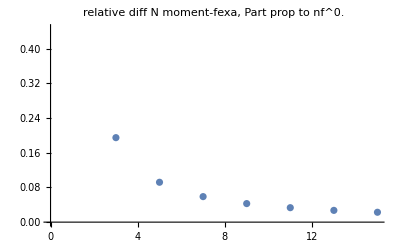

```mathematica
PlotNvals[{gqq3nspN2, gqq3nspN4, gqq3nspN6, gqq3nspN8,gqq3nspN10,gqq3nspN12,gqq3nspN14,gqq3nspN16}, Coefficient[gqq3nspexa,nf,0], 0, False, QCDConstantsRules]
```

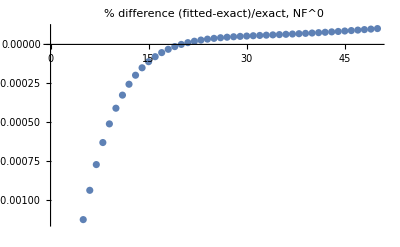

```mathematica
NF=0;
PlotRelativeDiff[Coefficient[gqq3nspexa,nf,NF], QCDConstantsRules, gqq3nspFitted + gqq3nspN0asy + gqq3nsNinf,QCDConstantsRules, NF,2,50]
```

#### NS, sea nf^1

1266.77+1743.23 x-4447.25 x^2+1437.25 x^3-127.315 Log[1-x]+127.315 x Log[1-x]+30.2 Log[1-x]^2-30.2 x Log[1-x]^2+2.19773 Log[1-x]^3-2.19773 x Log[1-x]^3+3337.72 Log[x]+1784.83 Log[x]^2+173.815 Log[x]^3+148.34 Log[x]^4+31.692 Log[x]^5

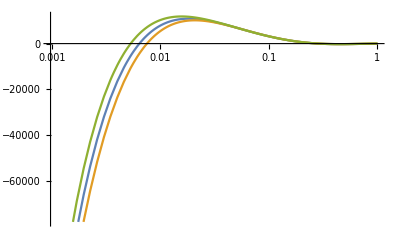

```mathematica
pqqnssnf1ref = (pqqnssnf1A + pqqnssnf1B)/2// Simplify //Expand
LogLinearPlot[{pqqnssnf1ref, pqqnssnf1A,pqqnssnf1B}, {x,0,1}]
```

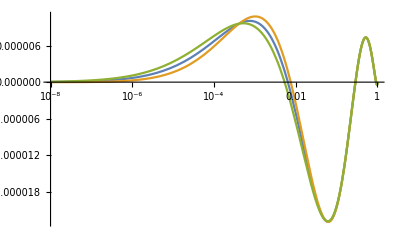

```mathematica
LogLinearPlot[{pqqnssnf1ref pifact , pqqnssnf1A pifact ,pqqnssnf1B pifact }, {x,0.00000001,1}]
```

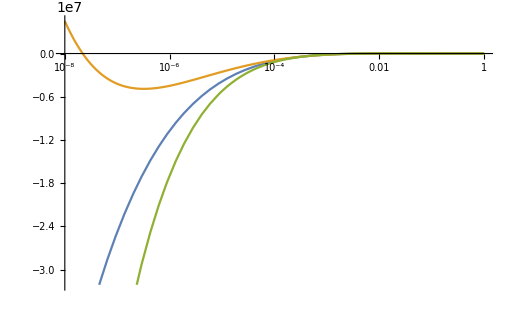

```mathematica
LogLinearPlot[{pqqnssnf1ref , pqqnssnf1A ,pqqnssnf1B }, {x,0.00000001,1}]
```

0.+3803.04/n^6-3560.16/n^5+1042.89/n^4-3569.65/n^3+3337.72/n^2-1266.77/n-1743.23/(1+n)+4447.25/(2+n)-1437.25/(3+n)-(127.315 (-1/(1+n)-S[1,n]))/(1+n)-(127.315 S[1,n])/n-(30.2 (S[1,n]^2+S[2,n]))/n+(30.2 (1/(1+n)^2+(1/(1+n)+S[1,n])^2+S[2,n]))/(1+n)+(2.19773 (S[1,n]^3+3 S[1,n] S[2,n]+2 S[3,n]))/n-(2.19773 ((1/(1+n)+S[1,n])^3+3 (1/(1+n)+S[1,n]) (1/(1+n)^2+S[2,n])+2 (1/(1+n)^3+S[3,n])))/(1+n)

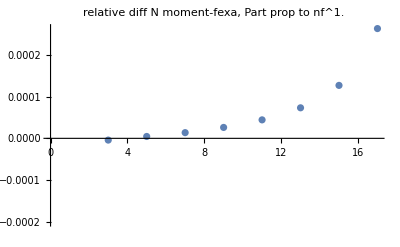

```mathematica
gqq3nssnf1 = - ((pqqnssnf1ref // Simplify //Expand ) - 1266.77 + 1266.77/n) /. MellinRules
PlotNvals[{gqq3nssN1, gqq3nssN3, gqq3nssN5, gqq3nssN7,gqq3nssN9,gqq3nssN11,gqq3nssN13,gqq3nssN15,gqq3nssN17}, gqq3nssnf1, 1, False, QCDConstantsRules]
```

```mathematica
pqqnssnf1A// Simplify
```

1607.73 (-1.+x) x (-3.10326+1. x)-60.4 (-1.+x) Log[1.-1. x]^2-4.685 (-1.+x) Log[1.-1. x]^3+3687.6 Log[x]+3296.6 Log[x]^2+1271.11 Log[x]^3+533.44 Log[x]^4+97.27 Log[x]^5+4 Log[x]^6

-2880/n^7+11672.4/n^6-12802.6/n^5+7626.66/n^4-6593.2/n^3+3687.6/n^2-4989.2/(1+n)+6596.93/(2+n)-1607.73/(3+n)-60.4 Log[1.-1./(1+n)]^2+(60.4 Log[1.-1./(1+n)]^2)/(1+n)-4.685 Log[1.-1./(1+n)]^3+(4.685 Log[1.-1./(1+n)]^3)/(1+n)

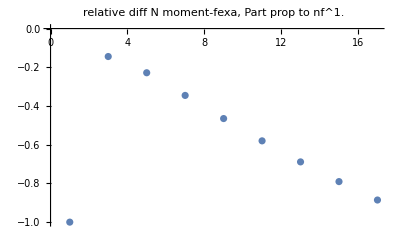

```mathematica
gqq3nssnf1A = - (pqqnssnf1A // Simplify //Expand)  /. MellinRules
PlotNvals[{gqq3nssN1, gqq3nssN3, gqq3nssN5, gqq3nssN7,gqq3nssN9,gqq3nssN11,gqq3nssN13,gqq3nssN15,gqq3nssN17}, gqq3nssnf1A, 1, False, QCDConstantsRules]
```

### Test quark number conservation

```mathematica
TestQuarkNumberConservation[f_, nftest_]:=Coefficient[f  /. n -> 1 //. QCDConstantsRules /. ZetaRules //N,nf, nftest];

TestQuarkNumberConservation[gqq3nsmFitted + gqq3nsmN0asy  + gqq3nsNinf, 0]
TestQuarkNumberConservation[gqq3nsmFitted + gqq3nsmN0asy  + gqq3nsNinf, 1]
TestQuarkNumberConservation[gqq3nsmFitted + gqq3nsmN0asy  + gqq3nsNinf, 2]
TestQuarkNumberConservation[gqq3nsmFitted + gqq3nsmN0asy  + gqq3nsNinf, 3]
gqq3nsmexa /. n -> 1
```

0.

-3.63798×10^-12

-5.68434×10^-14

8.88178×10^-16

-0.0205635-0.0521276 nf-0.0132667 nf^2-1.93757×10^-6 nf^3

### Check small x expansion

To compare with fig 1 sx of 2202.10362, to reproduce their results it is necessary to use the large nc limit constants.

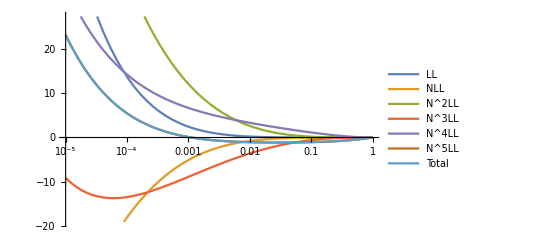

```mathematica
f5llomy=MellinInverse[gqq3nspN0asy, LargeNcQCDConstantsRules] //N;
f2llo = MellinInverse[Pns3R, LargeNcQCDConstantsRules]//N;
f3llo = MellinInverse[Pns3R + p33p  1/n^4, LargeNcQCDConstantsRules]//N;
f4llo = MellinInverse[Pns3R + p33p  1/n^4 + p34p  1/n^3, LargeNcQCDConstantsRules]//N;
f5llo = MellinInverse[Pns3R + p33p  1/n^4 + p34p  1/n^3+ p35p  1/n^2, LargeNcQCDConstantsRules]//N;
LogLinearPlot[{
1/(4Pi)^4 ((9 Log[x]^6)/16),
1/(4Pi)^4( (9 Log[x]^6)/16 +(18-(3 nf)/2) Log[x]^5)/. nf-> 4,
1/(4Pi)^4(f2llo)/. nf-> 4,
1/(4Pi)^4(f3llo)/. nf-> 4,
1/(4Pi)^4(f4llo)/. nf-> 4,
1/(4Pi)^4(f5llo)/. nf-> 4,
- 1/(4Pi)^4(f5llomy)/. nf-> 4
},{x,0.00001,1}, PlotLegends->{"LL", "NLL", "N^2LL", "N^3LL", "N^4LL","N^5LL", "Total"}]
```

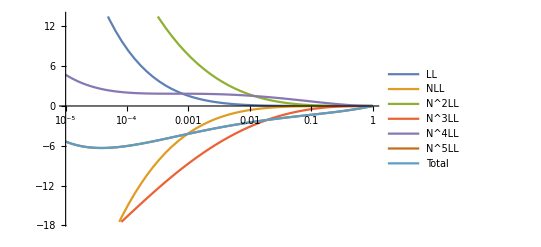

```mathematica
f5llomy=MellinInverse[gqq3nspN0asy, QCDConstantsRules] //N;
f2llo = MellinInverse[Pns3R, QCDConstantsRules]//N;
f3llo = MellinInverse[Pns3R + p33p  1/n^4, QCDConstantsRules]//N;
f4llo = MellinInverse[Pns3R + p33p  1/n^4 + p34p  1/n^3, QCDConstantsRules]//N;
f5llo = MellinInverse[Pns3R + p33p  1/n^4 + p34p  1/n^3+ p35p  1/n^2, QCDConstantsRules]//N;
LogLinearPlot[{
1/(4Pi)^4 (+0.3511659807956104 Log[x]^6),
1/(4Pi)^4 (+0.3511659807956104 Log[x]^6 +13.168724279835391 Log[x]^5-1.0534979423868314 nf Log[x]^5)/. nf-> 4,
1/(4Pi)^4 (f2llo)/. nf-> 4,
1/(4Pi)^4(f3llo)/. nf-> 4,
1/(4Pi)^4(f4llo)/. nf-> 4,
1/(4Pi)^4(f5llo)/. nf-> 4,
- 1/(4Pi)^4(f5llomy)/. nf-> 4
},{x,0.00001,1}, PlotLegends->{"LL", "NLL", "N^2LL", "N^3LL", "N^4LL","N^5LL", "Total"}]
```

### x Space nf^3 exact plot

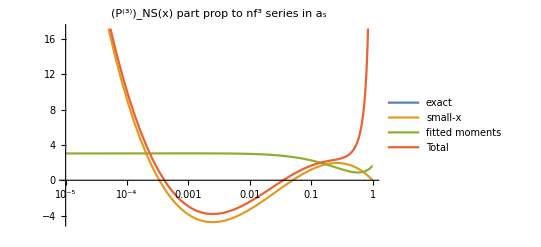

```mathematica
exactnf3 = MellinInverse[gqq3nsnf3, QCDConstantsRules];
smallx = MellinInverse[Coefficient[gqq3nsmN0asy,nf,3]];
fitted = MellinInverse[Coefficient[gqq3nsmFitted,nf,3]];
ffit = MellinInverse[Coefficient[gqq3nspFitted + gqq3nspN0asy + gqq3nsNinf,nf,3]];
xparam = -P3NSA3 - Coefficient[P3NSMB,nf,3] - Coefficient[P3NSMC,nf,3] Delta[1-x];
LogLinearPlot[
	{-exactnf3 /. Delta[__] -> 0, -smallx, -fitted/. Delta[__] -> 0, -ffit /. Delta[__] -> 0}, 
	{x, 0.00001, 1},
	PlotLabel->"(P^(3))_NS(x) part prop to nf^3 series in a_s",
	PlotLegends -> {"exact", "small-x", "fitted moments", "Total"}
]
```

```mathematica
seanf2 = Pns3Snf2 /. hrep //Simplify;
ffit = MellinInverse[Coefficient[gqq3nssFitted,nf,2]];
LogLinearPlot[{-seanf2 /. Delta[__] -> 0, -ffit /. Delta[__] -> 0}, {x, 0.0001, 1}]
```

$Aborted

### Plot fitted vs exact ns,+-

Power::infy: Infinite expression 1/0 encountered.

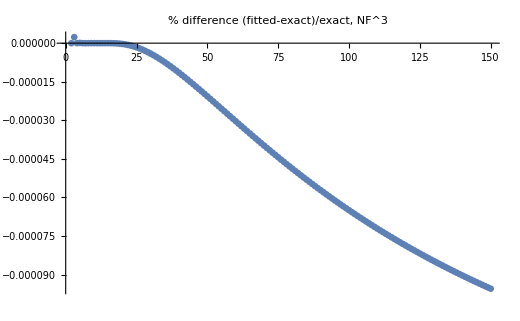

Power::infy: Infinite expression 1/0 encountered.

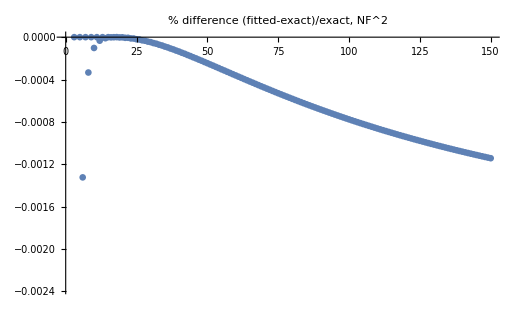

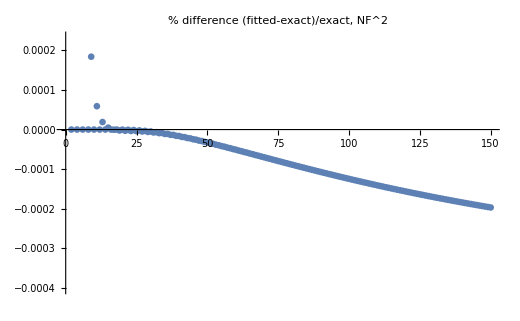

Power::infy: Infinite expression 1/0 encountered.

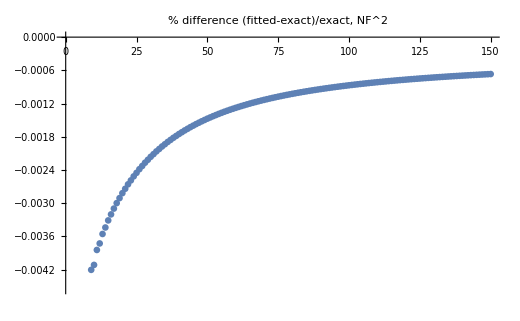

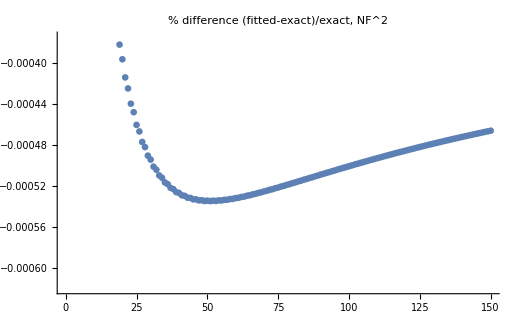

```mathematica
PlotRelativeDiff[gqq3nsnf3,  QCDConstantsRules, gqq3nspFitted + gqq3nspN0asy  + gqq3nsNinf, QCDConstantsRules, 3,1,150]
PlotRelativeDiff[gqq3nsmnf2, QCDConstantsRules, gqq3nsmFitted + gqq3nsmN0asy  + gqq3nsNinf, QCDConstantsRules, 2,1,150]
PlotRelativeDiff[gqq3nspnf2, QCDConstantsRules, gqq3nspFitted + gqq3nspN0asy  + gqq3nsNinf, QCDConstantsRules, 2,1,150]
PlotRelativeDiff[gqq3nsmnf2, QCDConstantsRules, gqq3nsmexa, QCDConstantsRules, 2,1,150]
PlotRelativeDiff[gqq3nspnf2, QCDConstantsRules, gqq3nspexa, QCDConstantsRules, 2,1,150]
```

#### Difference Ns,+ vs Ns,-

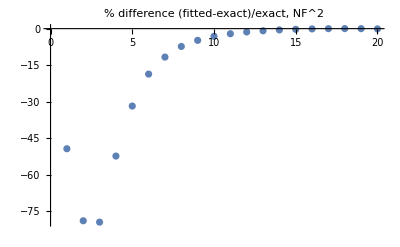

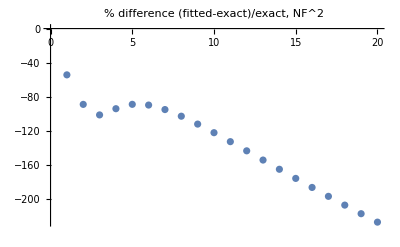

```mathematica
PlotRelativeDiff[cf(ca - 2 cf) (gqq3nsmnf2B - gqq3nspnf2B)  // Simplify, QCDConstantsRules,  gqq3nsmFitted - gqq3nspFitted, QCDConstantsRules, 2, 1, 20]
PlotRelativeDiff[cf(ca - 2 cf) (gqq3nsmnf2B - gqq3nspnf2B)  // Simplify, QCDConstantsRules,  gqq3nsmexa - gqq3nspexa, QCDConstantsRules, 2, 1, 20]
```

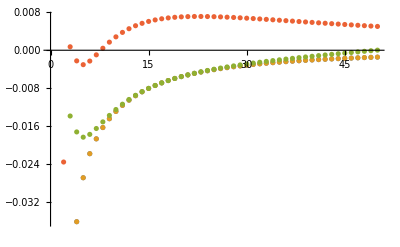

```mathematica
ListPlot[{
Table[gqq3nspnf2 - gqq3nsmnf2 /.QCDConstantsRules  //N //Simplify,{n,1,50}],
Table[cf (ca - 2 cf) (gqq3nspnf2B - gqq3nsmnf2B)/.QCDConstantsRules  //N //Simplify,{n,1,50}],
Table[Coefficient[ gqq3nspFitted -gqq3nsmFitted,nf,2] //Simplify, {n,1,50}],
Table[Coefficient[ gqq3nspexa -gqq3nsmexa,nf,2] //Simplify, {n,1,50}]
}]
```

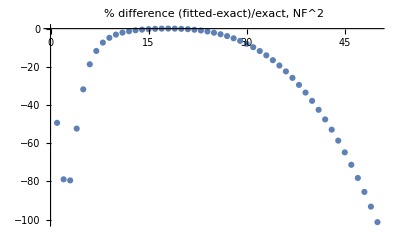

```mathematica
PlotRelativeDiff[(gqq3nspnf2 - gqq3nsmnf2) //Simplify , QCDConstantsRules,gqq3nspFitted-   gqq3nsmFitted , QCDConstantsRules, 2,1,50]
```

### Store results

```mathematica
(* ns,- *)
g3nsm := gqq3nsmFitted + gqq3nsmN0asy  + gqq3nsNinf /. QCDConstantsRules /. ZetaRules //N;
Save["/Users/giacomomagni/Documents/Wolfram Mathematica/Ad_N3LO/parametrised_ad/gnsm.m",g3nsm]

(* ns, +*)
g3nsp := gqq3nspFitted + gqq3nspN0asy  + gqq3nsNinf /. QCDConstantsRules /. ZetaRules //N;
Save["/Users/giacomomagni/Documents/Wolfram Mathematica/Ad_N3LO/parametrised_ad/gnsp.m",g3nsp]

(* ns, s*)
g3nss := nf gqq3nssnf1 + nf ^2 gqq3nssnf2 /. QCDConstantsRules /. ZetaRules //N;
Save["/Users/giacomomagni/Documents/Wolfram Mathematica/Ad_N3LO/parametrised_ad/gnss.m",g3nss]
```

```mathematica
Coefficient[gqq3nspFitted +  gqq3nspN0asy   + gqq3nsNinf /. QCDConstantsRules /. ZetaRules,nf,2]/.harmonics //N
```

-193.862-18.963/n^5+99.1605/n^4-226.441/n^3+395.605/n^2+278.221/n+59.4663/(1.+n)^3-152.704/(1.+n)^2-94.5721/(2.+n)+195.577 S1-(517.935 S1)/n^2+(26.6886 S1)/n+1.50065 Lm11m1[n]+113.483 Lm12m1[n]+13.8654 Lm13m1[n]

```mathematica
Coefficient[gqq3nspFitted + gqq3nspN0asy   + gqq3nsNinf /. QCDConstantsRules /. ZetaRules,nf,1]/.harmonics //N
```

5550.29-126.42/n^6+752.198/n^5-2253.11/n^4+5247.18/n^3-8769.15/n^2-5834.36/n+537.861/(1.+n)^3-718.387/(1.+n)^2+2487.96/(2.+n)-5171.92 S1+(12894.7 S1)/n^2-(2741.83 S1)/n-849.823 Lm11m1[n]-3106.33 Lm12m1[n]-399.222 Lm13m1[n]

```mathematica
Coefficient[gqq3nspFitted + gqq3nspN0asy  + gqq3nsNinf /. QCDConstantsRules /. ZetaRules,nf,0]/.harmonics //N
```

-23391.3-252.84/n^7+1580.25/n^6-5806.8/n^5+14899.9/n^4-28546.4/n^3+50759.7/n^2+21477.8/n+47399./(1.+n)^3-15176.3/(1.+n)^2-11103.4/(2.+n)+20702.4 S1-(73499. S1)/n^2+(16950.9 S1)/n-43731.1 Lm11m1[n]-2518.91 Lm12m1[n]-973.326 Lm13m1[n]

```mathematica
Coefficient[gqq3nsNinf,n,0] /. QCDConstantsRules /. ZetaRules //Expand //N
```

-23393.8+5550.04 nf-193.855 nf^2-3.01498 nf^3+20702.4 S[1.,n]-5171.92 nf S[1.,n]+195.577 nf^2 S[1.,n]+3.27234 nf^3 S[1.,n]